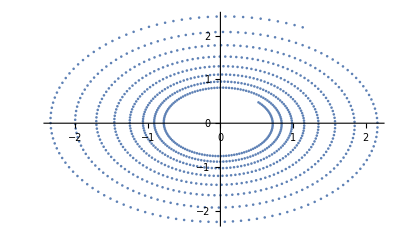

```mathematica
ClearAll["Global'*"]
name="out";
extension=".txt";
wayToFile="C:\\Users\\vbole\\OneDrive\\Рабочий стол\\Керил\\Study\\NumericMethodsForODU\\";
n =1;
fileList={};
For[i=0,i<n,i++;
fileList=Append[fileList,StringJoin[name,ToString[i],extension]];
]
plotList={};
For[i=0,i<Length[fileList],i++;
k=ReadList[StringJoin[wayToFile,fileList[[i]]],{Number,Number,Number}];
k1={};
For[j=1,j<Length[k],j++;
k1=Append[k1,{k[[j,2]],k[[j,3]]}];
];
plotList=Append[plotList,ListPlot[k1]];
];
Show[plotList]
```

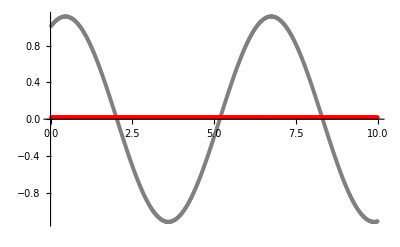

```mathematica
ClearAll["Global'*"]

k=ReadList[StringJoin[wayToFile,"Auto.txt"],{Number,Number,Number, Number}];
sol1={};
step={};
For[j=1,j<Length[k],j++;
sol1=Append[sol1,{k[[j,1]],k[[j,2]]}];
step=Append[step,{k[[j,1]],k[[j,4]]}];
];
plot1=ListPlot[sol1,PlotStyle->Gray];
plot2=ListPlot[step,PlotStyle->Red];
Show[plot1,plot2]
```